```mathematica
Charting`$InteractiveHighlighting=False
```

False

```mathematica
dat1=Import["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Cluster data/P2/outputO2/outputETOT.csv","Table"]//Flatten
```

{24.4871,-6.15164,-9.83918,-8.4155,-6.39093,-4.68474,-4.23425,-3.94909,-3.70156,-3.72284,-3.75421,-3.76573,-3.76886,-3.77241}

```mathematica
dattr=Transpose[{Range[0.75,4,0.25],dat1}]
```

{{0.75,24.4871},{1.,-6.15164},{1.25,-9.83918},{1.5,-8.4155},{1.75,-6.39093},{2.,-4.68474},{2.25,-4.23425},{2.5,-3.94909},{2.75,-3.70156},{3.,-3.72284},{3.25,-3.75421},{3.5,-3.76573},{3.75,-3.76886},{4.,-3.77241}}

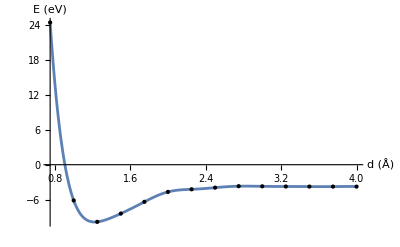

```mathematica
plt=Plot[Interpolation[dattr,Method->"Spline",InterpolationOrder->6][x],{x,0.75,4},Epilog->{Point[dattr]},PlotRange->All,AxesLabel->{"d (Å)","E (eV)"}]
```

```mathematica
Export["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/2/inplt.pdf",plt]
```

/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/2/inplt.pdf

```mathematica
eoccs=Import["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Cluster data/P2/outputO2/eOccs.tsv","Table"]
```

{{1.,1.,1.,1.,1.,1.,1.,0.,0.,0.,0.},{1.,1.,1.,1.,1.,0.,0.,0.,0.,0.,0.},{1.,1.,1.,1.,1.,1.,1.,0.,0.,0.,0.},{1.,1.,1.,1.,1.,0.,0.,0.,0.,0.,0.},{1.,1.,1.,1.,1.,1.,1.,0.,0.,0.,0.},{1.,1.,1.,1.,1.,0.,0.,0.,0.,0.,0.},{1.,1.,1.,1.,1.,1.,1.,0.,0.,0.,0.},{1.,1.,1.,1.,1.,0.,0.,0.,0.,0.,0.},{1.,1.,1.,1.,1.,1.,1.,0.,0.,0.,0.},{1.,1.,1.,1.,1.,0.,0.,0.,0.,0.,0.},{1.,1.,1.,1.,1.,1.,1.,0.,0.,0.,0.},{1.,1.,1.,1.,1.,0.,0.,0.,0.,0.,0.},{1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,0.},{1.,1.,1.,0.5,0.5,0.,0.,0.,0.,0.,0.},{1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,0.},{1.,1.,1.,0.5,0.5,0.,0.,0.,0.,0.,0.},{1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,0.},{1.,1.,1.,0.5,0.5,0.,0.,0.,0.,0.,0.},{1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,0.},{1.,1.,1.,1.,0.,0.,0.,0.,0.,0.,0.},{1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,0.},{1.,1.,1.,1.,0.,0.,0.,0.,0.,0.,0.},{1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,0.},{1.,1.,1.,1.,0.,0.,0.,0.,0.,0.,0.},{1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,0.},{1.,1.,1.,1.,0.,0.,0.,0.,0.,0.,0.},{1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,0.},{1.,1.,1.,1.,0.,0.,0.,0.,0.,0.,0.}}

```mathematica
upoccs=eoccs[[1;; ;;2]]
```

{{1.,1.,1.,1.,1.,1.,1.,0.,0.,0.,0.},{1.,1.,1.,1.,1.,1.,1.,0.,0.,0.,0.},{1.,1.,1.,1.,1.,1.,1.,0.,0.,0.,0.},{1.,1.,1.,1.,1.,1.,1.,0.,0.,0.,0.},{1.,1.,1.,1.,1.,1.,1.,0.,0.,0.,0.},{1.,1.,1.,1.,1.,1.,1.,0.,0.,0.,0.},{1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,0.},{1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,0.},{1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,0.},{1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,0.},{1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,0.},{1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,0.},{1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,0.},{1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,0.}}

```mathematica
downoccs=eoccs[[2;; ;;2]]
```

{{1.,1.,1.,1.,1.,0.,0.,0.,0.,0.,0.},{1.,1.,1.,1.,1.,0.,0.,0.,0.,0.,0.},{1.,1.,1.,1.,1.,0.,0.,0.,0.,0.,0.},{1.,1.,1.,1.,1.,0.,0.,0.,0.,0.,0.},{1.,1.,1.,1.,1.,0.,0.,0.,0.,0.,0.},{1.,1.,1.,1.,1.,0.,0.,0.,0.,0.,0.},{1.,1.,1.,0.5,0.5,0.,0.,0.,0.,0.,0.},{1.,1.,1.,0.5,0.5,0.,0.,0.,0.,0.,0.},{1.,1.,1.,0.5,0.5,0.,0.,0.,0.,0.,0.},{1.,1.,1.,1.,0.,0.,0.,0.,0.,0.,0.},{1.,1.,1.,1.,0.,0.,0.,0.,0.,0.,0.},{1.,1.,1.,1.,0.,0.,0.,0.,0.,0.,0.},{1.,1.,1.,1.,0.,0.,0.,0.,0.,0.,0.},{1.,1.,1.,1.,0.,0.,0.,0.,0.,0.,0.}}

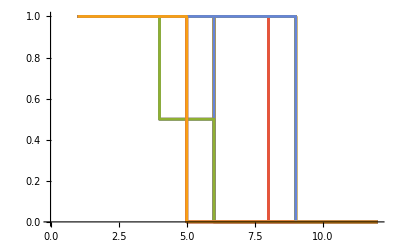

```mathematica
ListStepPlot[eoccs]
```

```mathematica
evals=Import[ToString@StringForm["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Cluster data/P2/outputO2/output``.csv",#],"Table"]&/@{"Up","Down"};
```

```mathematica
ev1=First@evals//Transpose;
```

```mathematica
ev1[[1]]//Length
```

14

```mathematica
Range[0.75,4,0.25]//Length
```

14

```mathematica
Length@evals
```

2

```mathematica
af=Table[Transpose[{Range[0.75,4,0.25],#}]&/@Transpose[f],{f,evals}];
```

```mathematica
pll=Table[Magnify[Plot[Interpolation[#,Method->"Spline"][x]&/@afi//Evaluate,{x,0.75,4},ImageSize->Medium,Epilog->{Point[#]&/@afi},AxesLabel->{"d (Å)","E (eV)"},PlotLabels->Range[1,11]],1.1],{afi,af}]
```

{-Graphics-,-Graphics-}

```mathematica
Export[ToString@StringForm["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/2/pllddep``.pdf",#2],#1]&@@@Transpose[{pll,{"Up","Down"}}]
```

{/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/2/pllddepUp.pdf,/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/2/pllddepDown.pdf}

```mathematica
g=Grid[Transpose@#,Frame->All]&/@evals
```

{-48.0271 | -38.6464 | -32.1518 | -28.4205 | -26.5744 | -25.6954 | -25.5355 | -25.3569 | -25.2723 | -24.9838 | -24.9929 | -25.0045 | -25.0143 | -25.0227
-22.5657 | -18.634 | -20.7367 | -22.4611 | -23.5686 | -24.1855 | -24.8064 | -24.9913 | -25.0868 | -24.8954 | -24.9479 | -24.981 | -25.0034 | -25.0162
-22.5657 | -16.0329 | -13.332 | -12.6671 | -11.948 | -11.3136 | -10.7532 | -10.4833 | -10.4259 | -10.6712 | -10.68 | -10.6894 | -10.6974 | -10.7036
-17.9865 | -16.0329 | -13.0857 | -11.5802 | -10.8203 | -10.4153 | -10.5892 | -10.4833 | -10.4259 | -10.6712 | -10.68 | -10.6894 | -10.6974 | -10.7036
-14.6835 | -13.9621 | -13.0857 | -11.5802 | -10.8203 | -10.4153 | -10.5892 | -10.4463 | -10.2568 | -10.5788 | -10.626 | -10.6573 | -10.6789 | -10.6921
-1.4345 | -4.5501 | -7.0188 | -8.3651 | -9.0829 | -9.4548 | -10.0677 | -10.1886 | -10.2568 | -10.5788 | -10.626 | -10.6573 | -10.6789 | -10.6921
-1.4345 | -4.5501 | -7.0188 | -8.3651 | -9.0829 | -9.4548 | -10.0677 | -10.1886 | -10.2332 | -8.8054 | -8.7376 | -8.6918 | -8.6684 | -8.6496
-0.7053 | -0.3613 | -0.4467 | -3.4485 | -6.2769 | -7.7641 | -8.5949 | -9.072 | -9.3639 | -8.1849 | -8.3315 | -8.4289 | -8.4876 | -8.5325
0.4701 | 0.9817 | 0.7003 | -0.3435 | -0.3598 | -0.3858 | -0.449 | -0.5036 | -0.5227 | -0.4857 | -0.4986 | -0.4953 | -0.5104 | -0.5224
0.4701 | 0.9902 | 1.0048 | 1.0516 | 1.0689 | 1.0672 | 1.011 | 1.0303 | 1.0212 | 1.0008 | 0.9868 | 0.9793 | 0.9663 | 0.9555
0.6012 | 0.9902 | 1.0048 | 1.1474 | 1.12 | 1.0727 | 1.1298 | 1.0837 | 1.0832 | 1.022 | 0.998 | 1.0043 | 0.9886 | 0.9778,-47.1717 | -37.6001 | -30.9149 | -27.0265 | -25.0783 | -24.1458 | -22.2449 | -22.0508 | -21.9598 | -21.3485 | -21.3455 | -21.3497 | -21.3556 | -21.3614
-20.9359 | -16.8854 | -18.9387 | -20.6676 | -21.8139 | -22.477 | -21.3759 | -21.595 | -21.7195 | -21.2168 | -21.2752 | -21.312 | -21.3357 | -21.3505
-20.9359 | -14.2261 | -12.4153 | -11.8921 | -11.2533 | -10.6514 | -8.3246 | -8.0009 | -7.7732 | -7.6014 | -7.5231 | -7.4687 | -7.4371 | -7.4138
-16.3469 | -14.2261 | -11.2413 | -9.7212 | -8.9479 | -8.534 | -7.2804 | -7.1621 | -7.0958 | -6.8793 | -7.0362 | -7.142 | -7.2093 | -7.258
-13.4618 | -12.8651 | -11.2413 | -9.7212 | -8.9479 | -8.534 | -7.2804 | -7.1621 | -7.0958 | -6.2697 | -6.2599 | -6.2564 | -6.2557 | -6.2565
-0.1623 | -2.2849 | -4.7493 | -6.1703 | -6.9657 | -7.4012 | -6.5632 | -6.7288 | -6.83 | -6.2697 | -6.2599 | -6.2564 | -6.2557 | -6.2565
0.5713 | -2.2849 | -4.7493 | -6.1703 | -6.9657 | -7.4012 | -6.5632 | -6.7288 | -6.83 | -6.0819 | -6.1394 | -6.1784 | -6.2046 | -6.2223
0.5714 | -0.1563 | -0.341 | -2.5024 | -5.4094 | -6.9506 | -5.7494 | -6.2999 | -6.6488 | -6.0819 | -6.1394 | -6.1784 | -6.2046 | -6.2223
1.1254 | 1.2452 | 0.9967 | -0.2817 | -0.3172 | -0.3494 | -0.3068 | -0.2857 | -0.3014 | -0.2561 | -0.2618 | -0.2659 | -0.2735 | -0.2855
1.1254 | 1.2452 | 1.1243 | 1.1025 | 1.1842 | 1.1165 | 1.1989 | 1.1956 | 1.1677 | 1.1286 | 1.1169 | 1.1368 | 1.1222 | 1.1168
1.2845 | 1.2689 | 1.1245 | 1.2121 | 1.1944 | 1.1276 | 1.2165 | 1.2335 | 1.23 | 1.2719 | 1.2874 | 1.3003 | 1.3238 | 1.2917}

```mathematica
h=Column[{#3,Spacer[1],Row[{Spacer[225],#1,Spacer[50],#2}]}]&@@@Transpose[{mat,pll,g}]
```

Transpose::nmtx: The first two levels of … cannot be transposed.

Transpose[{-48.0271 | -38.6464 | -32.1518 | -28.4205 | -26.5744 | -25.6954 | -25.5355 | -25.3569 | -25.2723 | -24.9838 | -24.9929 | -25.0045 | -25.0143 | -25.0227
-22.5657 | -18.634 | -20.7367 | -22.4611 | -23.5686 | -24.1855 | -24.8064 | -24.9913 | -25.0868 | -24.8954 | -24.9479 | -24.981 | -25.0034 | -25.0162
-22.5657 | -16.0329 | -13.332 | -12.6671 | -11.948 | -11.3136 | -10.7532 | -10.4833 | -10.4259 | -10.6712 | -10.68 | -10.6894 | -10.6974 | -10.7036
-17.9865 | -16.0329 | -13.0857 | -11.5802 | -10.8203 | -10.4153 | -10.5892 | -10.4833 | -10.4259 | -10.6712 | -10.68 | -10.6894 | -10.6974 | -10.7036
-14.6835 | -13.9621 | -13.0857 | -11.5802 | -10.8203 | -10.4153 | -10.5892 | -10.4463 | -10.2568 | -10.5788 | -10.626 | -10.6573 | -10.6789 | -10.6921
-1.4345 | -4.5501 | -7.0188 | -8.3651 | -9.0829 | -9.4548 | -10.0677 | -10.1886 | -10.2568 | -10.5788 | -10.626 | -10.6573 | -10.6789 | -10.6921
-1.4345 | -4.5501 | -7.0188 | -8.3651 | -9.0829 | -9.4548 | -10.0677 | -10.1886 | -10.2332 | -8.8054 | -8.7376 | -8.6918 | -8.6684 | -8.6496
-0.7053 | -0.3613 | -0.4467 | -3.4485 | -6.2769 | -7.7641 | -8.5949 | -9.072 | -9.3639 | -8.1849 | -8.3315 | -8.4289 | -8.4876 | -8.5325
0.4701 | 0.9817 | 0.7003 | -0.3435 | -0.3598 | -0.3858 | -0.449 | -0.5036 | -0.5227 | -0.4857 | -0.4986 | -0.4953 | -0.5104 | -0.5224
0.4701 | 0.9902 | 1.0048 | 1.0516 | 1.0689 | 1.0672 | 1.011 | 1.0303 | 1.0212 | 1.0008 | 0.9868 | 0.9793 | 0.9663 | 0.9555
0.6012 | 0.9902 | 1.0048 | 1.1474 | 1.12 | 1.0727 | 1.1298 | 1.0837 | 1.0832 | 1.022 | 0.998 | 1.0043 | 0.9886 | 0.9778,-47.1717 | -37.6001 | -30.9149 | -27.0265 | -25.0783 | -24.1458 | -22.2449 | -22.0508 | -21.9598 | -21.3485 | -21.3455 | -21.3497 | -21.3556 | -21.3614
-20.9359 | -16.8854 | -18.9387 | -20.6676 | -21.8139 | -22.477 | -21.3759 | -21.595 | -21.7195 | -21.2168 | -21.2752 | -21.312 | -21.3357 | -21.3505
-20.9359 | -14.2261 | -12.4153 | -11.8921 | -11.2533 | -10.6514 | -8.3246 | -8.0009 | -7.7732 | -7.6014 | -7.5231 | -7.4687 | -7.4371 | -7.4138
-16.3469 | -14.2261 | -11.2413 | -9.7212 | -8.9479 | -8.534 | -7.2804 | -7.1621 | -7.0958 | -6.8793 | -7.0362 | -7.142 | -7.2093 | -7.258
-13.4618 | -12.8651 | -11.2413 | -9.7212 | -8.9479 | -8.534 | -7.2804 | -7.1621 | -7.0958 | -6.2697 | -6.2599 | -6.2564 | -6.2557 | -6.2565
-0.1623 | -2.2849 | -4.7493 | -6.1703 | -6.9657 | -7.4012 | -6.5632 | -6.7288 | -6.83 | -6.2697 | -6.2599 | -6.2564 | -6.2557 | -6.2565
0.5713 | -2.2849 | -4.7493 | -6.1703 | -6.9657 | -7.4012 | -6.5632 | -6.7288 | -6.83 | -6.0819 | -6.1394 | -6.1784 | -6.2046 | -6.2223
0.5714 | -0.1563 | -0.341 | -2.5024 | -5.4094 | -6.9506 | -5.7494 | -6.2999 | -6.6488 | -6.0819 | -6.1394 | -6.1784 | -6.2046 | -6.2223
1.1254 | 1.2452 | 0.9967 | -0.2817 | -0.3172 | -0.3494 | -0.3068 | -0.2857 | -0.3014 | -0.2561 | -0.2618 | -0.2659 | -0.2735 | -0.2855
1.1254 | 1.2452 | 1.1243 | 1.1025 | 1.1842 | 1.1165 | 1.1989 | 1.1956 | 1.1677 | 1.1286 | 1.1169 | 1.1368 | 1.1222 | 1.1168
1.2845 | 1.2689 | 1.1245 | 1.2121 | 1.1944 | 1.1276 | 1.2165 | 1.2335 | 1.23 | 1.2719 | 1.2874 | 1.3003 | 1.3238 | 1.2917}

mat{-Graphics-,-Graphics-}]

```mathematica
Export[ToString@StringForm["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/2/pllddep``.pdf",#2],Magnify[#1,0.7]]&@@@Transpose[{h,{"Up","Down"}}]
```

Transpose::nmtx: The first two levels of {Transpose[{Grid[{{«14»},{«14»},{«14»},{«14»},{«14»},{«14»},{«14»},{«14»},{«14»},{«14»},«1»},Frame→All],Grid[{{«14»},{«14»},{«14»},{«14»},{«14»},{«14»},{«14»},{«14»},{«14»},{«14»},«1»},Frame→All]}
1
225],{Up,Down}} cannot be transposed.

Transpose[/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/2/pllddep{Up, Down}.pdf]

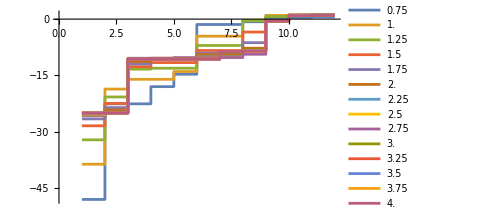
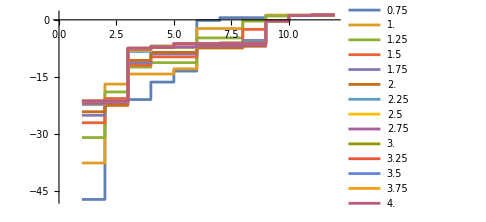

```mathematica
ListStepPlot[#//Evaluate,PlotLegends->Range[0.75,4,0.25],ImageSize->Medium]&/@evals
```

```mathematica
v=SparseArray@Transpose@Rationalize[eoccs]
```

SparseArray[…]

```mathematica
Grid[v]
```

1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1/2 | 1 | 1/2 | 1 | 1/2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1/2 | 1 | 1/2 | 1 | 1/2 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

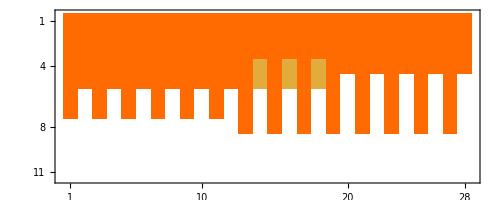

```mathematica
MatrixPlot[v]
```

```mathematica
mat=Grid[Transpose[#]//Rationalize,Frame->All]&/@{upoccs,downoccs}
```

{1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0,1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1/2 | 1/2 | 1/2 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1/2 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0}

```mathematica
Export[ToString@StringForm["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/2/occsTab``.pdf",#2],#1]&@@@Transpose[{mat,{"Up","Down"}}]
```

{/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/2/occsTabUp.pdf,/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/2/occsTabDown.pdf}

```mathematica
ListStepPlot[#,PlotLegends->Range[0.75,4,0.25],PlotRange->{-0.1,All}]&/@eoccs;
```

```mathematica
Export["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/2/occsTab.pdf",mat]
```

/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/2/occsTab.pdf

```mathematica
ArrayPlot@Transpose@eoccs//Export["",#]&
```

Export::chtype: First argument "" is not a valid file specification.

$Failed

```mathematica
Export["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/2/occsMat.pdf",MatrixPlot[v]]
```

/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/2/occsMat.pdf

## Part 2 molecules

```mathematica
data=Dataset[Import[ToString@StringForm["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Cluster data/P2/potfit/outputETOT``.csv",#],"Table","HeaderLines"->0,"FieldSeparators"->"\t","NumberPoint"->".",CharacterEncoding->"UTF8"]][All,Range[1,1]][All,Rule@@@Transpose[{ToString@StringForm["Band ``",#]&/@Range[1,1]//Evaluate,Range[1,1]}]//Association]&/@{"o2","co","no"};
```

```mathematica
data2=Transpose[{Apply[Range,#2],#1[All,ToString@StringForm["Band 1"]]}//Normal//Evaluate]&@@@Transpose[{data,{{1.08, 1.32,0.024},{1.02, 1.24,0.022},{1.03,  1.27,0.024}}}];
```

```mathematica
Range[1.08, 1.32,0.024 ]//Length
```

11

```mathematica
j={5,5,5};
```

```mathematica
ip=Table[Interpolation[di,InterpolationOrder->5,Method->"Spline"],{di,data2}];
```

```mathematica
fits=Fit[#,{1,x,x^2},x]&/@(Take[#1,{#2,-1}]&@@@Transpose[{data2,j}])
```

{42.0008-81.7954 x+32.9733 x^2,45.9296-106.08 x+46.3356 x^2,45.7045-98.2047 x+41.8319 x^2}

```mathematica
Factor/@fits
```

{32.9733 (-1.75475+1. x) (-0.725906+1. x),46.3356 (-1.70957+1. x) (-0.579817+1. x),41.8319 (-1.70787+1. x) (-0.639729+1. x)}

```mathematica
coeffs=Fit[#,{1,x,x^2},x,"BestFitParameters"]&/@(Take[#1,{#2,-1}]&@@@Transpose[{data2,j}]);
```

```mathematica
mins=Round[FindMinimum[#,{x,1.25},AccuracyGoal->3][[2]][[1]][[2]]&/@fits,0.001]
```

{1.24,1.145,1.174}

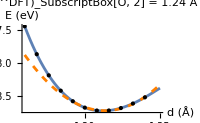
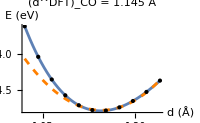
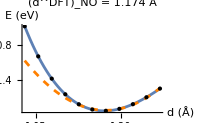

```mathematica
fpl=Show[Plot[#1[d],{d,#3[[1]],#3[[2]]},ImageSize->200,Epilog->{Point[#]&/@#2},PlotRange->All,AxesLabel->{"d (Å)","E (eV)"}],Plot[#4,{x,#3[[1]],#3[[2]]},PlotStyle->{Orange,Dashed},PlotRange->All],PlotLabel->StringForm["(d^DFT)_(``) = `` Å",#5,#6]]&@@@Transpose[{ip,data2,{{1.08,1.35},{1.02, 1.24},{1.03,1.27}},fits,{"O_2","CO","NO"},mins}]
```

```mathematica
expmins={1.201,1.128,1.151};
(#1-#2)/#2&@@@Transpose[{mins,expmins}]//PercentForm
```

{3.247%,1.507%,1.998%}

```mathematica
Export["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/2/fitpltssss.pdf",Row[fpl]]
```

/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/2/fitpltssss.pdf

```mathematica
Around[1.151,1.151/10]
```

1.150.12

```mathematica
Range[1.15-0.12,1.15+0.12,0.24/10]
```

{1.03,1.054,1.078,1.102,1.126,1.15,1.174,1.198,1.222,1.246,1.27}

```mathematica
%//Length
```

11

```mathematica
0.24/10
```

0.024

```mathematica
ClearAll[h]
```

```mathematica
f=NonlinearModelFit[With[{b=RandomReal[{0,3},3500]},Transpose[{b,Table[#,{x,b}]}]],k/2(x-x0)^2+h,{k,x0,h},x]&/@fits
```

{FittedModel[-8.72571+32.9733 (-1.24033+x)^2],FittedModel[-14.785+46.3356 (-1.14469+x)^2],FittedModel[-11.9318+41.8319 (-1.1738+x)^2]}

```mathematica
#["BestFitParameters"][[1]][[2]]&/@f
```

{65.9466,92.6713,83.6638}

```mathematica
ks=Quantity[1/10^-20#["BestFitParameters"][[1]][[2]]&/@f,("Electronvolts")/("Meters"^2)]//UnitConvert[#,"SIBase"]&
```

{1056.58 kg/s^2,1484.76 kg/s^2,1340.44 kg/s^2}

```mathematica
Quantity[1/10^-20#["BestFitParameters"][[1]][[2]]&/@f,("Electronvolts")/("Meters"^2)]
```

{6.59466×10^21 eV/m^2,9.26713×10^21 eV/m^2,8.36638×10^21 eV/m^2}

```mathematica
UnitConvert[Quantity[8.33, "Electronvolts"], "SIBase"]//N
```

1.33461×10^-18 kg m^2/s^2

```mathematica
Quantity[1,"Meters"/"Seconds"]
```

1 m/s

```mathematica
RandomReal[{1,3},15]
```

{2.65869,1.75308,1.09004,2.0141,1.48962,2.70147,2.0409,2.72572,2.87519,2.06763,2.1376,2.64415,2.14392,2.10934,1.02023}

```mathematica
mus=UnitConvert[#,"Kilograms"]&/@{Quantity[7.9995, "AtomicMassUnit"],Quantity[6.8605, "AtomicMassUnit"],Quantity[7.4684, "AtomicMassUnit"]}
```

{1.32835×10^-26 kg,1.13921×10^-26 kg,1.24016×10^-26 kg}

```mathematica
nus=√(#1/#2)1/(2π)&@@@Transpose[{ks,mus}]/10^12//Round[#,0.1]&
```

{44.9 per second,57.5 per second,52.3 per second}

```mathematica
100(#1-#2)/#2&@@@Transpose[{{47.4,65.1,59.3},nus}]//Round[#,0.01]&
```

{Round[(47.4+-44.9 per second) (2.22717 s),0.01],Round[(65.1+-57.5 per second) (1.73913 s),0.01],Round[(59.3+-52.3 per second) (1.91205 s),0.01]}

```mathematica
QuantityMagnitude@Quantity[1, "Terahertz"]
```

1

Failure[…]

```mathematica
k=1192.28;
dk=0.49;
mu=1.32 10^-26;
dd=D[√(kk/mu),kk]/.{kk->k}
√((dd dk)^2)/10^12
```

1.26036×10^11

0.0617575

## Bond order pt3

```mathematica
{d1,corr,mol}=Import["/Users/giovannigravili/Downloads/dati.txt.txt","Table"]//Transpose
```

{{0.121703,0.182656,0.130626,0.125691,0.1503,0.13544},{-0.00170271,-0.0626556,-0.0106262,-0.00569094,-0.0302999,-0.0154405},{O2,Li2,F2,C2,Be2,B2}}

```mathematica
dat=d1-corr
```

{0.123405,0.245311,0.141252,0.131382,0.1806,0.150881}

```mathematica
{b,mol2}=Import["/Users/giovannigravili/Downloads/bond.txt.txt","Table"]//Transpose
```

{{2,1,1,2,0,1},{O2,Li2,F2,C2,Be2,B2}}

```mathematica
mol==mol2
```

True

```mathematica
mol={"O_2","Li_2","F_2","C_2","Be_2","B_2"}
```

{O_2,Li_2,F_2,C_2,Be_2,B_2}

```mathematica
g=SortBy[Transpose[{b,dat,mol}],First]
```

{{0,0.1806,Be_2},{1,0.141252,F_2},{1,0.150881,B_2},{1,0.245311,Li_2},{2,0.123405,O_2},{2,0.131382,C_2}}

```mathematica
lbl=#3&@@@g
```

{Be_2,F_2,B_2,Li_2,O_2,C_2}

```mathematica
plsst=ListPlot[SortBy[Transpose[{b,dat}],First]//Partition[#,1]&,PlotLabels->lbl,ImageSize->Medium,AxesLabel->{"Bond order","Bond length (Å)"},Ticks->{Range[0,2,1],Automatic}]
```

-Graphics-

```mathematica
Export["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/2/boplt.pdf",plsst]
```

/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/2/boplt.pdf